```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY187/sec_int_data/368nm.dat"]
```

{{1.45287,-0.778052},{1.39708,-0.990933},{1.35876,-1.1542},{1.32403,-1.27347},{1.28662,-1.35089},{1.25869,-1.44189},{1.22636,-1.44202},{1.19613,-1.39699},{1.17366,-1.43953},{1.15413,-1.65459},{1.12528,-1.87425},{1.11495,-1.49482},{1.10625,-1.46516},{1.09912,-1.36207},{1.09306,-1.22898},{1.0888,-1.16146},{1.08648,-1.20467},{1.08572,-1.28468},{1.08632,-1.75406},{1.0888,-1.85202},{1.09505,-1.32554},{1.09559,-1.23922},{1.12528,-1.01735},{1.14263,-0.85144},{1.16354,-0.735909},{1.19414,-0.694889},{1.22405,-0.652639},{1.25343,-0.638867},{1.28081,-0.654888},{1.31748,-0.639568},{1.36987,-0.665124},{1.42194,-0.686092},{1.47153,-0.728029},{1.11308,-0.985159}}

-3.22189+1.71469 x

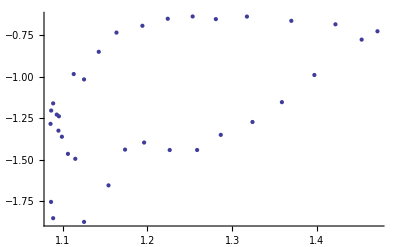

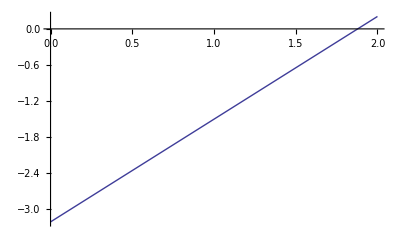

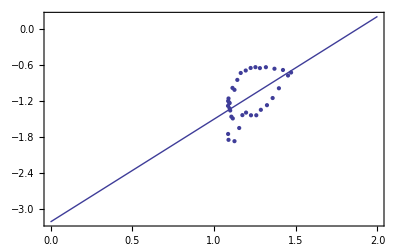

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```